```mathematica
iris=Import["https://gist.githubusercontent.com/curran/a08a1080b88344b0c8a7/raw/0e7a9b0a5d22642a06d3d5b9bcbad9890c8ee534/iris.csv"];
```

```mathematica
irisnorm=Transpose[Standardize[iris⟦2;;,#⟧]&/@Range@4];
```

```mathematica
(* SPLOM *)
(*Grid[Table[If[i≠j,ListPlot[Partition[irisnorm⟦All,{i,j}⟧,50],PlotMarkers->{"•",20},AspectRatio->1,Frame->True],""],{i,1,4},{j,1,4}]]*)
```

```mathematica
distmat=DistanceMatrix[irisnorm];
```

```mathematica
(*distmat=DistanceMatrix[#]*AdjacencyMatrix[NearestNeighborGraph[#,70]]&[irisnorm+RandomReal[{-0.001,0.001},{150,4}]];*)
```

## t-SNE

```mathematica
pT[j_,i_,σ_]:=Exp[-distmat⟦i,j⟧^2/(2 σ^2)]/Sum[Boole[k≠i]*Exp[-distmat⟦i,k⟧^2/(2 σ^2)],{k,1,Length[distmat]}]
```

```mathematica
pTFast[j_,i_,σ_]:=Exp[-distmat⟦i,j⟧^2/(2 σ^2)]/(Total@Exp[-distmat⟦i⟧^2/(2 σ^2)]-1)
```

```mathematica
h[i_,σ_]:=-Sum[pT[j,i,σ]Log[2,pT[j,i,σ]],{j,1,Length@distmat}]
```

```mathematica
hFast[i_,σ_]:=-Total[#*Log[2,#]&[pTFast[#,i,σ]&/@Range@Length@distmat]]
```

```mathematica
Timing[Do[h[1,5.],100]]
```

{11.7188,Null}

```mathematica
Timing[Do[hFast[1,5.],100]]
```

{0.15625,Null}

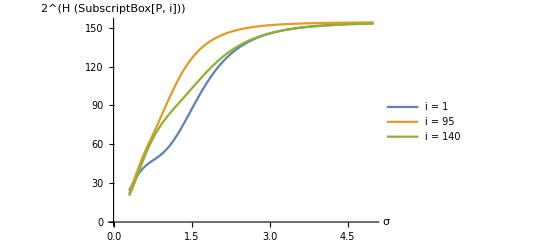

```mathematica
ListLinePlot[
Table[{σ,2^hFast[#,N@σ]},{σ,0.3,5,0.01}]&/@{1,95,140}
,AxesLabel->{"σ","2^(H (SubscriptBox[P, i]))"}
,PlotLegends->{"i = 1","i = 95","i = 140"}
]
```

```mathematica
entropy=Compile[{{d,_Real,1},{β,_Real}},Module[{x=-d*β,y,ysum},
y=Exp[-d*β];
ysum=Total@y-1;
If[ysum<10^-10,Print["Error!"];-1,
(-Total[y*x-y*Log[ysum]])/(Log[2]*ysum)
]]]
```

CompiledFunction[…]

```mathematica
foo=entropy[#,1/(2*5.^2)]&/@(distmat^2);
```

```mathematica
bar=hFast[#,5.]&/@Range@Length@distmat;
```

```mathematica
pTFast[10,12,1.]
```

0.0225308

General::munfl: Exp[-724.892] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-837.12] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-712.785] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

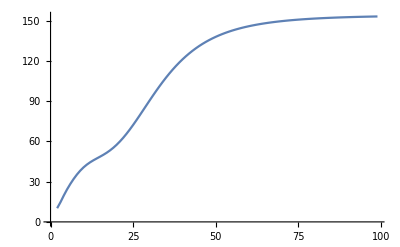

```mathematica
ListLinePlot[2^hFast[1,#]&/@Range[0.1,5,0.05]]
```

```mathematica
perp[i_Integer,σ_?NumericQ]:=2^entropy[distmat⟦i⟧^2,1/(2*σ^2)]
```

```mathematica
sigmasT=Flatten[(id↦FindRoot[perp[id,#]-70&,{1.}])/@Range@Length@distmat];
```

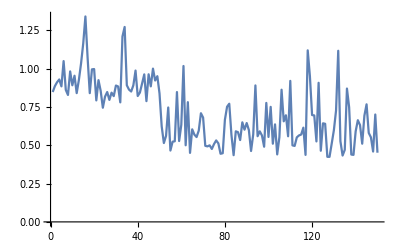

```mathematica
ListLinePlot[sigmasT]
```

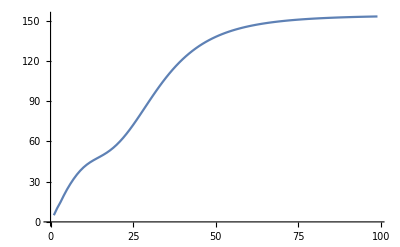

```mathematica
ListLinePlot[2^entropy[distmat[[1]]^2,1/(2*#^2)]&/@Range[0.1,5,0.05]]
```

```mathematica
pTFast[1,1,5]
```

0.00801506

```mathematica
pMatT=Table[pTFast[j,i,sigmasT⟦i⟧],{i,Range@Length@distmat},{j,Range@Length@distmat}]ᵀ;
```

```mathematica
pMatTSym=(pMatT+pMatTᵀ)/(2*Length@distmat);
```

```mathematica
Row[{MatrixPlot[pMatT,ImageSize->500],MatrixPlot[pMatTSym,ImageSize->500]}]
```

## UMAP

```mathematica
pU[j_,i_,σ_]:=If[distmat⟦i,j⟧==0.,0.,Exp[-(distmat⟦i,j⟧^2-Min[DeleteCases[Drop[distmat⟦i⟧,{i}]^2,0.]])/σ]]
```

```mathematica
pUSum[i_,σ_?NumericQ]:=Total@Exp[-(distmat⟦i⟧^2-Min[Drop[distmat⟦i⟧],{i}]^2)/σ]
```

```mathematica
pUSum2[i_,σ_?NumericQ]:=Total@Table[pU[j,i,σ],{j,1,Length@distmat}]
```

```mathematica
sigmasU=Flatten[(id↦FindRoot[pUSum[id,#]-Log[2,70]&,{0.1}])/@Range@Length@distmat];
```

```mathematica
sigmasU=Flatten[(id↦FindRoot[pUSum2[id,#]-Log[2,70]&,{0.1}])/@Range@Length@distmat];
```

```mathematica
sigmasU
```

{0.113189,0.154524,0.138209,0.142511,0.175446,0.392768,0.243036,0.109029,0.419343,0.112959,0.252206,0.155643,0.155179,0.412246,0.814804,1.95954,0.400869,0.113052,0.494434,0.261381,0.229075,0.221595,0.416948,0.236595,0.197793,0.208016,0.141239,0.125088,0.126487,0.136776,0.106048,0.239587,0.769068,1.00141,0.112657,0.168262,0.276988,0.112574,0.2837,0.107254,0.129388,2.07305,0.267438,0.270845,0.327658,0.177971,0.278131,0.155259,0.218444,0.139598,0.517067,0.328335,0.340815,0.501329,0.250426,0.2039,0.410465,0.814333,0.271448,0.445834,1.49681,0.222834,0.779374,0.182396,0.310389,0.314125,0.267735,0.282304,0.740932,0.275725,0.393025,0.237936,0.407512,0.244008,0.237607,0.253531,0.386351,0.254884,0.180106,0.357367,0.358843,0.402743,0.21729,0.261425,0.384044,0.63353,0.26973,0.636382,0.263111,0.304522,0.291404,0.207895,0.245538,0.8081,0.216916,0.265187,0.182112,0.202599,0.666148,0.184456,0.550867,0.330788,0.366186,0.259896,0.279461,0.767136,0.90589,0.559604,0.662951,1.21453,0.286459,0.296653,0.242315,0.570752,0.624486,0.312533,0.242217,2.19775,1.50761,0.744456,0.295152,0.426755,0.981825,0.26392,0.341117,0.528344,0.230649,0.231852,0.316465,0.502792,0.63324,2.37024,0.358438,0.231726,0.435327,0.868111,0.549288,0.269598,0.244082,0.251174,0.270992,0.318703,0.330136,0.292138,0.415191,0.283539,0.454054,0.227115,0.56259,0.278885}

```mathematica
pMatU=Chop@Table[pU[j,i,sigmasU⟦i⟧],{i,Range@Length@distmat},{j,Range@Length@distmat}]ᵀ;
```

```mathematica
pMatUSym=(pMatU+pMatUᵀ)-(pMatU*pMatUᵀ);
```

```mathematica
Row[{MatrixPlot[pMatU,ImageSize->500],MatrixPlot[pMatUSym,ImageSize->500]}]
```

```mathematica
ConnectedGraphQ@WeightedAdjacencyGraph[pMatUSym]
```

True

```mathematica
dU=DiagonalMatrix[1/√Total[pMatUSym]];
```

```mathematica
{eval,evec}=Eigensystem[IdentityMatrix[Length@pMatUSym]-dU.pMatUSym.dU ];
```

```mathematica
ListPlot[Partition[evec⟦2;;3⟧ᵀ,50]]
```

```mathematica
umapResult=Import["D:\\Dokumente\\Dissertation\\Code\\Python\\ptsne-pytorch\\foo.csv"][[2;;,2;;]];
```

```mathematica
tsneResult=DimensionReduce[irisnorm,Method->{"TSNE","Perplexity"->70}];
```

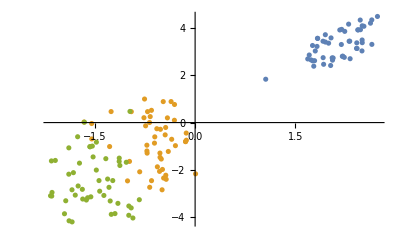

```mathematica
ListPlot[Partition[tsneResult,50]]
```

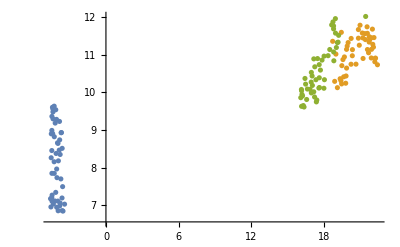

```mathematica
ListPlot[Partition[umapResult,50]]
```

```mathematica
qT=#/(Total[#]-1)&[1/(1+DistanceMatrix[tsneResult]^2)];
```

```mathematica
MatrixPlot[qT]
```

```mathematica
MatrixPlot[pMatTSym]
```

```mathematica
minDist=0.1;
spread=1.;
```

```mathematica
xv=Range[0,3,0.01];
```

```mathematica
yv=If[#<minDist,1.,Exp[-(#-0.1)/spread]]&/@xv;
```

```mathematica
fit=FindFit[{xv,yv}ᵀ,{1/(1+a*x^(2b)),{a>0,b>0}},{a,b},x,Gradient->"FiniteDifference"]
```

{a→1.57694,b→0.895062}

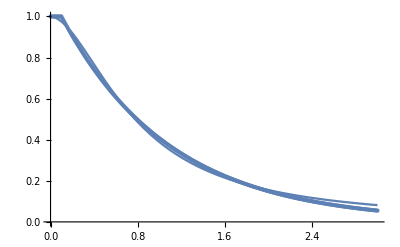

```mathematica
Show[Plot[1/(1+a*x^(2b))/.fit,{x,0,3}],ListPlot[{xv,yv}ᵀ]]
```

```mathematica
qU=1/(1+a*#^(2b))/.fit&/@DistanceMatrix[umapResult];
```

```mathematica
MatrixPlot[qU]
```

```mathematica
MatrixPlot[pMatUSym]
```